## Attempts at Getting Chern Number

1. First we Visualize the Surface

```mathematica
Manipulate[
ParametricPlot3D[{{Sin[px],Sin[py],2-m-c*Cos[px]-d*Cos[py]},{px,py,0}},{px,-π,π},{py,-π,0},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-4,4}}
],
{m,-5,5},{c,0,2},{d,0,2}
]
```

```mathematica
ParametricPlot3D[{{Sin[px],Sin[py],2-1-Cos[px]-Cos[py]}},{px,-π,π},{py,-π,π},
PlotLabel->"m="<>ToString[1],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
pic1=Table[
ParametricPlot3D[{{Sin[px],Sin[py],2-m-Cos[px]-Cos[py]},{px,py,0}},{px,-π,π},{py,-π,π},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-4,4}},PlotLabel->"m="<>ToString[m]
],
{m,-1,5,1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListPointPlot3D[
ParallelTable[ {Sin[px],Sin[py],2-1-Cos[px]-Cos[py]},{px,-π,π,0.05},{py,-π,π,0.05}],AxesLabel->{x,y,z}
]
```

-Graphics3D-

2. Next we Calculate the Chern Number

2.1 Method 1: Dispatch the surface into four bands

```mathematica
f11[x_,y_,m_]:=2-m+√(1-x^2)+√(1-y^2);
f12[x_,y_,m_]:=2-m+√(1-x^2)-√(1-y^2);
f21[x_,y_,m_]:=2-m-√(1-x^2)+√(1-y^2);
f22[x_,y_,m_]:=2-m-√(1-x^2)-√(1-y^2);
f11x[x_,y_,m_]:={1,0,D[f11[x,y,m],x]};
f11y[x_,y_,m_]:={0,1,D[f11[x,y,m],y]};
numerator11[x_,y_,m_]:=Cross[f11x[x,y,m],f11y[x,y,m]].{x,y,f11[x,y,m]}
denominator11[x_,y_,m_]:=(x^2+y^2+f11[x,y,m]^2)^(3/2);

f12x[x_,y_,m_]:={1,0,D[f12[x,y,m],x]};
f12y[x_,y_,m_]:={0,1,D[f12[x,y,m],y]};
numerator12[x_,y_,m_]:=Cross[f12x[x,y,m],f12y[x,y,m]].{x,y,f12[x,y,m]}
denominator12[x_,y_,m_]:=(x^2+y^2+f12[x,y,m]^2)^(3/2);

f21x[x_,y_,m_]:={1,0,D[f21[x,y,m],x]};
f21y[x_,y_,m_]:={0,1,D[f21[x,y,m],y]};
numerator21[x_,y_,m_]:=Cross[f21x[x,y,m],f21y[x,y,m]].{x,y,f21[x,y,m]}
denominator21[x_,y_,m_]:=(x^2+y^2+f21[x,y,m]^2)^(3/2);

f22x[x_,y_,m_]:={1,0,D[f22[x,y,m],x]};
f22y[x_,y_,m_]:={0,1,D[f22[x,y,m],y]};
numerator22[x_,y_,m_]:=Cross[f22x[x,y,m],f22y[x,y,m]].{x,y,f22[x,y,m]}
denominator22[x_,y_,m_]:=(x^2+y^2+f22[x,y,m]^2)^(3/2);
ChernNumber[m_]:=(NIntegrate[numerator11[x,y,m]/denominator11[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator12[x,y,m]/denominator12[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator21[x,y,m]/denominator21[x,y,m],{x,-1,1},{y,-1,1}]+NIntegrate[numerator22[x,y,m]/denominator22[x,y,m],{x,-1,1},{y,-1,1}])/(4π);
```

Numerical Integration (failed)

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

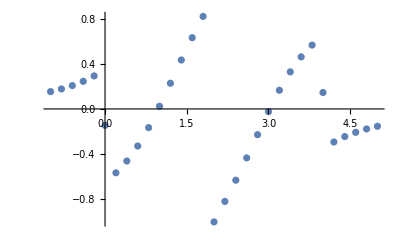

```mathematica
ListPlot[
ParallelTable[{m,ChernNumber[m]},{m,-1,5,0.2}]
]
```

Visualization and Imagination

```mathematica
Manipulate[
{Plot3D[{f11[x,y,m],f12[x,y,m],f21[x,y,m],f22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Red, Blue,Green,Yellow}
],
Plot3D[{f11[x,y,m],f22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Red,Yellow}
],
Plot3D[{f12[x,y,m],f21[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-2.5,2.5}},BoxRatios->{3, 3, 5},PlotStyle->{Blue,Green}
]
},
{m,2,5}
]
```

Visualization with Normalized to sphere

```mathematica
normalization[px_,py_,m_]:=Norm[{Sin[px],Sin[py],2-m-Cos[px]-Cos[py]}];
```

```mathematica
Manipulate[
ParametricPlot3D[{{Sin[px]/normalization[px,py,m],Sin[py]/normalization[px,py,m],(2-m-Cos[px]-Cos[py])/normalization[px,py,m]},{px,py,0}},{px,-π,π},{py,-π,π},
AxesLabel->{x,y,z}, PlotRange->{{-1.5,1.5},{-1.5,1.5},{-5,5}}
],
{m,-5,5}
]
```

```mathematica
normalizedf11[x_,y_,m_]:={x,y,f11[x,y,m]}/Sqrt[x^2+y^2+f11[x,y,m]^2];
normalizedf12[x_,y_,m_]:={x,y,f12[x,y,m]}/Sqrt[x^2+y^2+f12[x,y,m]^2];
normalizedf21[x_,y_,m_]:={x,y,f21[x,y,m]}/Sqrt[x^2+y^2+f21[x,y,m]^2];
normalizedf22[x_,y_,m_]:={x,y,f22[x,y,m]}/Sqrt[x^2+y^2+f22[x,y,m]^2];
```

```mathematica
Manipulate[
ParametricPlot3D[{normalizedf11[x,y,m],normalizedf12[x,y,m],normalizedf21[x,y,m],normalizedf22[x,y,m]},{x,-1,1},{y,-1,1},
AxesLabel->{x,y,z}
],
{m,-5,5}
]
```

```mathematica
patches=GraphicsGrid[{{ParametricPlot3D[normalizedf11[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf12[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf21[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}],ParametricPlot3D[normalizedf22[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->{x,y,z}]}},
ImageSize->Large
]
```

-Graphics-

2.2 Method 2: Calculate with S.S.Qing’s formula

Formulae available in p.23 of Shen Shun-Qing’s Topological Insulator

```mathematica
d[px_,py_,m_]:={Sin[px],Sin[py],2-m-Cos[px]-Cos[py]};
integrandD[px_,py_,m_]:=Dot[
Cross[D[d[px,py,m],px],D[d[px,py,m],py]],
d[px,py,m]]/(Norm[d[px,py,m]]^(3))
```

```mathematica
integrandD[px,py,m]
```

(Cos[px] (2-m-Cos[px]-Cos[py]) Cos[py]-Cos[py] Sin[px]^2-Cos[px] Sin[py]^2)/((Abs[2-m-Cos[px]-Cos[py]]^2+Abs[Sin[px]]^2+Abs[Sin[py]]^2)^(3/2))

```mathematica
ChernNumber3[m_]:=NIntegrate[integrandD[px,py,m],{px,-π,π},{py,-π,π}]/(4*π);
```

```mathematica
listOfChernN=ParallelTable[
{m,ChernNumber3[m]},{m,-1,5,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.36634×10^-9 and 3.62031×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.41052×10^-14 and 3.96614×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.8957×10^-17 and 2.46913×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.90372×10^-14 and 2.32305×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.81394×10^-16 and 2.73896×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.25693×10^-15 and 2.68191×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.17265×10^-17 and 6.78955×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.30047×10^-15 and 7.02484×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.27005×10^-15 and 2.68×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.61506×10^-15 and 2.73731×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.48064×10^-17 and 4.55314×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.51155×10^-16 and 5.99121×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.01362×10^-15 and 4.54563×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{-1.,-6.2832×10^-18},{-0.9,2.52471×10^-18},{-0.8,-4.36136×10^-18},{-0.7,2.0312×10^-17},{-0.6,1.27905×10^-17},{-0.5,-5.65801×10^-17},{-0.4,1.88308×10^-10},{-0.3,-5.42236×10^-17},{-0.2,-1.80645×10^-16},{-0.1,-4.32239×10^-15},{1.11022×10^-16,-0.5},{0.1,-1.},{0.2,-1.},{0.3,-1.},{0.4,-1.},{0.5,-1.},{0.6,-1.},{0.7,-1.},{0.8,-1.},{0.9,-1.},{1.,-1.},{1.1,-1.},{1.2,-1.},{1.3,-1.},{1.4,-1.},{1.5,-1.},{1.6,-1.},{1.7,-1.},{1.8,-1.},{1.9,-1.},{2.,-3.90225×10^-15},{2.1,1.},{2.2,1.},{2.3,1.},{2.4,1.},{2.5,1.},{2.6,1.},{2.7,1.},{2.8,1.},{2.9,1.},{3.,1.},{3.1,1.},{3.2,1.},{3.3,1.},{3.4,1.},{3.5,1.},{3.6,1.},{3.7,1.},{3.8,1.},{3.9,1.},{4.,0.5},{4.1,-6.69288×10^-15},{4.2,4.18333×10^-16},{4.3,-4.46832×10^-16},{4.4,-2.97179×10^-17},{4.5,8.40127×10^-17},{4.6,1.03488×10^-16},{4.7,1.99863×10^-17},{4.8,8.06614×10^-17},{4.9,4.3425×10^-17},{5.,2.3443×10^-17}}

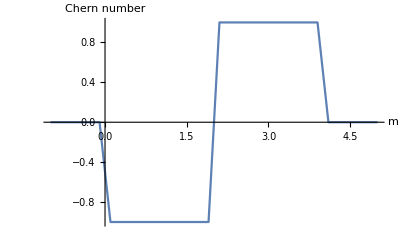

```mathematica
ListPlot[Sort[listOfChernN],AxesLabel->{m,"Chern number"},Joined->True]
```